### Importing and interpolations

```mathematica
SetDirectory[NotebookDirectory[]];
{ffdata["Mean"],ffdata["Unc"]}=Import[#,"Table"]&/@{"FFproton_UAmodel.txt","FFproton_UAmodel_Uncertainty.txt"};
Flatten[ffdata["Mean"][[#]]&/@Range[1,7],1];
Flatten[ffdata["Unc"][[#]]&/@Range[1,7],1];
strrepl[argument_]:=ToExpression[StringReplace[ToString[argument],{"+-"->"-","j"->"*I"}]]
ffdata["Mean"]={#[[1]],strrepl[#[[2]]],strrepl[#[[3]]]}&/@Drop[ffdata["Mean"],7];
ffdata["Unc"]={#[[1]],strrepl[#[[2]]],strrepl[#[[3]]],strrepl[#[[4]]],strrepl[#[[5]]]}&/@Drop[ffdata["Unc"],7];
intdata[data_]:=If[mX<Max[data[[All,1]]],Evaluate[10^Interpolation[{Log10[#[[1]]+10^-90],Log10[#[[2]]]}&/@data,InterpolationOrder->1][Log10[mX]]],0.];
{F1centralInt[mX_],F1lowerInt[mX_],F1upperInt[mX_],F2centralInt[mX_],F2lowerInt[mX_],F2upperInt[mX_]}=intdata[#]&/@{ffdata["Mean"][[All,{1,2}]],ffdata["Unc"][[All,{1,2}]],ffdata["Unc"][[All,{1,3}]],ffdata["Mean"][[All,{1,3}]],ffdata["Unc"][[All,{1,4}]],ffdata["Unc"][[All,{1,5}]]};
LogLogPlot[Evaluate[{Abs[F1upperInt[mx]],Abs[F1lowerInt[mx]],Abs[F1centralInt[mx]]}],{mx,0.02,1.99},PlotPoints->500];
```

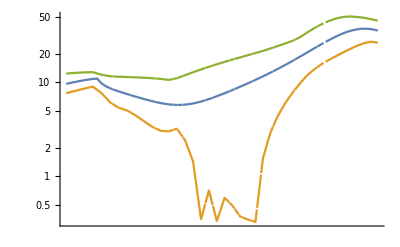

```mathematica
LogLogPlot[{Abs[F2centralInt[mX]],Abs[F2lowerInt[mX]],Abs[F2upperInt[mX]]},{mX,1.3,1.7}]
```

### Extrapolations for the individual form-factors

```mathematica
{F1lowerExtrapolation[mX_],F1centralExtrapolation[mX_],F1upperExtrapolation[mX_],F2lowerExtrapolation[mX_],F2centralExtrapolation[mX_],F2upperExtrapolation[mX_]}=If[mX<1.989,Evaluate[#[mX]],Evaluate[#[1.989](1.989/mX)^12]]&/@{F1lowerInt,F1centralInt,F1upperInt,F2lowerInt,F2centralInt,F2upperInt};
Export["FR-form-factors-total.mx",{F1lowerExtrapolation[mX],F1centralExtrapolation[mX],F1upperExtrapolation[mX],F2lowerExtrapolation[mX],F2centralExtrapolation[mX],F2upperExtrapolation[mX]},"MX"]
```

FR-form-factors-total.mx

### XXX

```mathematica
rd=Import["FR-form-factors-total.mx","MX"];
rd[[1]]/.{mX->1.5}
rd[[2]]/.{mX->1.5}
rd[[3]]/.{mX->1.5}
rd[[4]]/.{mX->1.5}
```

0.623605+1.61015 ⅈ

1.8194+4.51681 ⅈ

4.72788+7.31962 ⅈ

-0.489807-0.00501645 ⅈ